```mathematica
SetDirectory[SystemDialogInput["Directory"]]
```

C:\Users\86177\Desktop\innovation\valon program

```mathematica
ParentDirectory["C:\\Users\\86177\\Desktop"]
```

C:\Users\86177

```mathematica
<<"ListData.mx"
```

```mathematica
Listlabel=Join[Partition[DownValues[ListData][[All,1]][[All,1,1]],1],
Partition[DownValues[ListData][[All,1]][[All,1,2]],1],2]
```

{{antiomega,0-10%},{antiomega,10-20%},{antiomega,20-40%},{antiomega,40-60%},{antiomega,60-80%},{k0s,0-5%},{k0s,10-20%},{k0s,20-30%},{k0s,30-40%},{k0s,40-60%},{k0s,5-10%},{k0s,60-80%},{ka-,0-5%},{ka-,10-20%},{ka-,20-30%},{ka-,30-40%},{ka-,40-50%},{ka-,50-60%},{ka-,5-10%},{ka-,60-70%},{ka-,70-80%},{ka+,0-5%},{ka+,10-20%},{ka+,20-30%},{ka+,30-40%},{ka+,40-50%},{ka+,50-60%},{ka+,5-10%},{ka+,60-70%},{ka+,70-80%},{lambda,0-5%},{lambda,10-20%},{lambda,20-30%},{lambda,30-40%},{lambda,40-60%},{lambda,5-10%},{lambda,60-80%},{lambdabar,0-5%},{lambdabar,10-20%},{lambdabar,20-30%},{lambdabar,30-40%},{lambdabar,40-60%},{lambdabar,5-10%},{lambdabar,60-80%},{omega,0-10%},{omega,10-20%},{omega,20-40%},{omega,40-60%},{omega,60-80%},{pbar,0-5%},{pbar,10-20%},{pbar,20-30%},{pbar,30-40%},{pbar,40-50%},{pbar,50-60%},{pbar,5-10%},{pbar,60-70%},{pbar,70-80%},{phi,0-10%},{phi,10-20%},{phi,20-40%},{phi,40-60%},{phi,60-80%},{pi-,0-5%},{pi-,10-20%},{pi-,20-30%},{pi-,30-40%},{pi-,40-50%},{pi-,50-60%},{pi-,5-10%},{pi-,60-70%},{pi-,70-80%},{pi+,0-5%},{pi+,10-20%},{pi+,20-30%},{pi+,30-40%},{pi+,40-50%},{pi+,50-60%},{pi+,5-10%},{pi+,60-70%},{pi+,70-80%},{proton,0-5%},{proton,10-20%},{proton,20-30%},{proton,30-40%},{proton,40-50%},{proton,50-60%},{proton,5-10%},{proton,60-70%},{proton,70-80%},{xi,0-5%},{xi,10-20%},{xi,20-30%},{xi,30-40%},{xi,40-60%},{xi,5-10%},{xi,60-80%},{xibar,0-5%},{xibar,10-20%},{xibar,20-30%},{xibar,30-40%},{xibar,40-60%},{xibar,5-10%},{xibar,60-80%}}

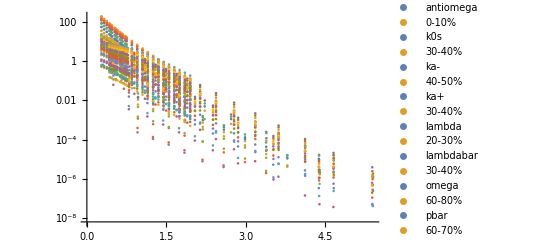

```mathematica
ListLogPlot[ListData@@@Listlabel,PlotLegends->Listlabel]
```

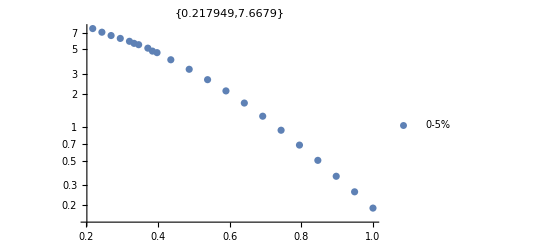

```mathematica
particlename="proton";
Select[Listlabel,#[[1]]==particlename&&#[[2]]=="0-5%"&];
Map[{#[[1]]/1.95,#[[2]]}&,ListData@@@%,{2}];
data=ListLogPlot[%,PlotRange->Full,PlotLabel->%[[1,1]],PlotLegends->%%[[All,2]]]
```